### 計算結果のアニメーション’

```mathematica
ClearAll["Global`*"];
(*dataE=Import[FileNameJoin[{NotebookDirectory[],"cable_euler.json"}]];
timeE="time"/.dataE;
positionE="position"/.dataE;*)

(*dataRK4=Import[FileNameJoin[{NotebookDirectory[],"cable_rk4.json"}]];
timeRK4="time"/.dataRK4;
positionRK4="position"/.dataRK4;*)

dataL=Import[FileNameJoin[{NotebookDirectory[],"cable_leapfrog_K14E7_NL0d5.json"}]];
timeL="time"/.dataL;
positionL="position"/.dataL;
tensionL="tension"/.dataL;

r=70;(*plot range*)
max=1;

frame[n_]:=Labeled[
Row[
Table[
Graphics3D[
{
(*{Red,Line[positionE[[n]]]},
{Red,Point[positionE[[n]]]},*)
{Black,Line[positionL[[n]]]},
{Black,Point[positionL[[n]]]}(*,
{Green,Line[positionRK4[[n]]]},
{Green,Point[positionRK4[[n]]]}*)
},
BoxRatios->{1,1,1},
LabelStyle->{Large,FontFamily->"Times"},
PlotRange->{{-r/2,r/2},{-r/2,r/2},{-5,5}},
Axes->True,
AxesLabel->{x,y,z},
AxesStyle->{Red,Green,Blue},
ImageSize->Medium,
BoxStyle->Directive[Black],
ViewPoint->view],
{view,{{0,-2,0},{-2,0,0}}}]
],
Style["time="<>ToString[timeL[[n]]]<>"\nMin="<>ToString[Min[positionL[[n]]],TraditionalForm]<>"\ntension"<>ToString[MinMax[tensionL[[n]]]]]
]

frames=Table[frame[n],{n,1,Length[positionL],10}];
(*Manipulate[frames[[n]],{n,1,Length[frames],1}]*)

(*GIFを作る場合*)
(*Export[FileNameJoin[{NotebookDirectory[],"sample.gif"}],frames,
"DisplayDurations"->0.025,
"TransparentColor"->None,
"AnimationRepetitions"->10,
"CompressionLevel"->.1];*)
```

```mathematica
(*(*3Dベクトル場をプロット*)
Manipulate[
arrows={Arrowheads[.01],Arrow[{#1,#1+#2/10000}]}&@@@Transpose[{positionL[[n]],tensionL[[n]]}];
Graphics3D[arrows,
Axes->True,
BoxRatios->{1,1,1},
PlotRange->{{-r/2,r/2},{-r/2,r/2},{-5,5}}],
{n,1,Length[frames],1}]*)
```

### 節点間距離を変えて計算結果の2Dプロット

```mathematica
(*繰り返し使うプロットオプション*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]];
```

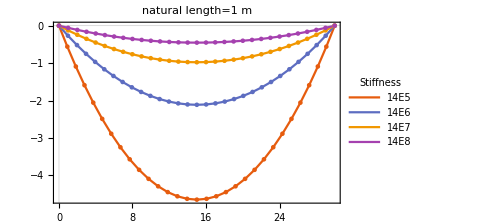
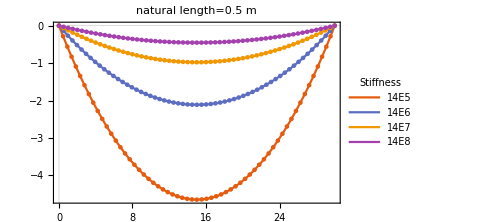

```mathematica
(*最後の時刻のデータを抽出する関数*)
getPosition[filename_]:=Module[{dataL},
dataL=Import[FileNameJoin[{NotebookDirectory[],filename}]];
(*timeL=("time"/.dataL)[[-1]];*)
positionL={#1,#3}&@@@("position"/.dataL)[[-1]];
(*tensionL=("tension"/.dataL)[[-1]];*)
Return[positionL];
]

(*自然長を変えた結果を並べてプロット*)
Row[
{f1=ListPlot[
{getPosition["cable_leapfrog_K14E5_NL1d0.json"],
getPosition["cable_leapfrog_K14E6_NL1d0.json"],
getPosition["cable_leapfrog_K14E7_NL1d0.json"],
getPosition["cable_leapfrog_K14E8_NL1d0.json"]},
PlotLabel->"natural length=1 m",
PlotLegends->LineLegend[{"14E5","14E6","14E7","14E8"},LegendLabel->"Stiffness"],
Evaluate[plot2Doption],
Mesh->All]
,
f2=ListPlot[
{getPosition["cable_leapfrog_K14E5_NL0d5.json"],
getPosition["cable_leapfrog_K14E6_NL0d5.json"],
getPosition["cable_leapfrog_K14E7_NL0d5.json"],
getPosition["cable_leapfrog_K14E8_NL0d5.json"]},
PlotLabel->"natural length=0.5 m",
PlotLegends->LineLegend[{"14E5","14E6","14E7","14E8"},LegendLabel->"Stiffness"],
Evaluate[plot2Doption],
Mesh->All]
}]
```

### カテナリー曲線の解y[x]=aCosh[x/a]

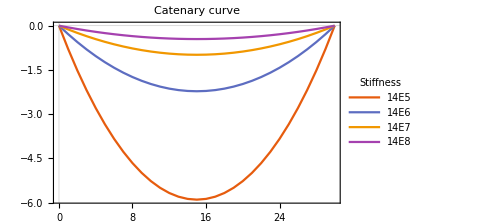

```mathematica
(*カテナリー曲線をプロット．ただし計算結果に対応させるためには，計算結果の端部の水平張力が必要なので抽出している*)
(*カテナリー曲線*)
diameter=132*10^-3;
A=π*(diameter/2)^2;
K=1400*10^3;
e=K/A;
w=348.5;(*kg/m*)
g=9.81;
a=e*A/(w*g);
a=78834.8/(w*g);

getCatenaryCurve[filename_,{Xstart_,Xend_}]:=Module[{dataL,v1to2,H0,a},
dataL=Import[FileNameJoin[{NotebookDirectory[],filename}]];
(*timeL=("time"/.dataL)[[-1]];*)
positionL={#1,#3}&@@@("position"/.dataL)[[-1]];
v1to2=positionL[[2]]-positionL[[1]];
H0=Abs[Max[("tension"/.dataL)[[-1]]]*Dot[v1to2,{1,0}]/Norm[v1to2]];
a=H0/(w*g);
Return[Table[{x+(Xend-Xstart)/2,a*(Cosh[x/a]-Cosh[Xend/a])},{x,Xstart,Xend}]];
]
ListPlot[
{getCatenaryCurve["cable_leapfrog_K14E5_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E6_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E7_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E8_NL0d5.json",{-15,15}]},
PlotLabel->"Catenary curve",
PlotLegends->LineLegend[{"14E5","14E6","14E7","14E8"},LegendLabel->"Stiffness"],
Evaluate[plot2Doption]]
```

### シミュレーション結果とカテナリー曲線との比較

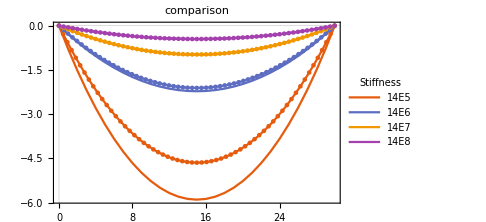

```mathematica
(*定常状態に至ったシミュレーションの結果と，カテナリー曲線を比較*)
Show[ListPlot[
{getCatenaryCurve["cable_leapfrog_K14E5_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E6_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E7_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E8_NL0d5.json",{-15,15}]},
Evaluate[plot2Doption],
PlotLabel->"comparison",
PlotLegends->LineLegend[{"14E5","14E6","14E7","14E8"},LegendLabel->"Stiffness"]
],
ListPlot[
{getPosition["cable_leapfrog_K14E5_NL0d5.json"],
getPosition["cable_leapfrog_K14E6_NL0d5.json"],
getPosition["cable_leapfrog_K14E7_NL0d5.json"],
getPosition["cable_leapfrog_K14E8_NL0d5.json"]}
,Mesh->All
,Evaluate[plot2Doption]
]]
```

```mathematica
(*カテナリー曲線*)
diameter=132*10^-3;
A=π*(diameter/2)^2;
K=1400*10^3;
e=K/A;
w=348.5;(*kg/m*)
g=9.81;
a=e*A/(w*g);
a=78834.8/(w*g);

getCatenaryCurve[filename_,{Xstart_,Xend_}]:=Module[{dataL,v1to2,H0,a},
dataL=Import[FileNameJoin[{NotebookDirectory[],filename}]];
(*timeL=("time"/.dataL)[[-1]];*)
positionL={#1,#3}&@@@("position"/.dataL)[[-1]];
v1to2=positionL[[2]]-positionL[[1]];
H0=Abs[Max[("tension"/.dataL)[[-1]]]*Dot[v1to2,{1,0}]/Norm[v1to2]];
a=H0/(w*g);
Return[Table[{x+(Xend-Xstart)/2,a*(Cosh[x/a]-Cosh[Xend/a])},{x,Xstart,Xend}]];
]
ListPlot[
{getCatenaryCurve["cable_leapfrog_K14E5_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E6_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E7_NL0d5.json",{-15,15}],
getCatenaryCurve["cable_leapfrog_K14E8_NL0d5.json",{-15,15}]},
PlotLabel->"Catenary curve",
PlotLegends->LineLegend[{"14E5","14E6","14E7","14E8"},LegendLabel->"Stiffness"],
Evaluate[plot2Doption]]
```

-Graphics-

0.367159

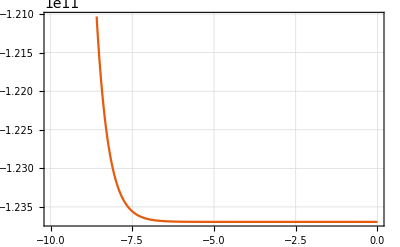

```mathematica
g=9.81;
T0=1600*10^3;
(*T0=280000*10^3;*)
rho=7850;
diameter=0.15;
(*diameter=0.92;*)
A=π*(diameter/2)^2;
w=rho/A;
a=T0/(w*g)
Xend=-10;
Plot[a*Cosh[x/a]-a*Cosh[Xend/a],{x,Xend,Xend+10},PlotTheme->"Scientific",GridLines->Automatic]
```